# Infinite 3D medium, Isotropic Point Source, Rayleigh Scattering

## Gamma-6 Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine
b - anisotropy parameter

### Namespace

```mathematica
Begin["inf3DisopointRayleighscatterGamma6`"]
```

inf3DisopointRayleighscatterGamma6`

## Analytical results

### Collision rate density

collision rate density Cc due to correlated emission:

#### derivation

```mathematica
Clear[c];pc[s_]:=c 1/120 ⅇ^-s s^5
```

```mathematica
f00=Fpc[0,0,pc];
f01=Fpc[0,1,pc];
f11=Fpc[1,1,pc];
f20=Fpc[2,0,pc];
f22=Fpc[2,2,pc];
```

```mathematica
o=3;
Clear[A,b,c,r,h,F];
A[n_]:=0;
A[0]:=1;
A[1]:=0;
A[2]:=1/2;
hsystem=Table[h[k]==2/Pi u F[k,0]+ Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.F[0,0]->f00/.F[0,1]->f01/.F[1,1]->f11/.F[1,0]->-f01/.F[2,0]->f20/.F[0,2]->f20/.F[2,2]->f22]
```

{{h[0]→-(2 c u (c (1-10 u^2+u^4)-2 (1+u^2)^3 (5-10 u^2+u^4)))/(π (10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4))),h[1]→(4 c u^2 (c (1-3 u^2)^2 (-5+3 u^2)-5 (1+u^2)^5 (-10+6 u^2-7 u F[1,2]+u^3 F[1,2])))/(5 π (1+u^2)^2 (10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4))),h[2]→-(8 c (-7+u^2) (u+u^3)^3)/(π (10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4)))}}

```mathematica
Clear[r,c];(2k+1)1/(4 Pi c)(h[k])u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify
```

{-(u^2 (c (1-10 u^2+u^4)-2 (1+u^2)^3 (5-10 u^2+u^4)) Sinc[r u])/(2 π^2 (10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4)))}

#### result

```mathematica
Ccexact[r_,c_]:=NIntegrate[-(u^2 (c (1-10 u^2+u^4)-2 (1+u^2)^3 (5-10 u^2+u^4)) Sinc[r u])/(2 π^2 (10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4))),{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
With[{c=0.8},
Integrate[-(u^2 (c (1-10 u^2+u^4)-2 (1+u^2)^3 (5-10 u^2+u^4)) Sinc[r u])/(2 π^2 (10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4))),{u,0,Infinity},Assumptions->r>0]//Chop//FullSimplify
]
```

-1/r((0.0154486-0.0119228 ⅈ) ⅇ^((-1.51445+0.359146 ⅈ) r)+(0.0154486+0.0119228 ⅈ) ⅇ^((-1.51445-0.359146 ⅈ) r)+(0.00281184-0.0070784 ⅈ) ⅇ^((-1.15928+0.217661 ⅈ) r)+(0.00281184+0.0070784 ⅈ) ⅇ^((-1.15928-0.217661 ⅈ) r)-(0.00972-0.0156929 ⅈ) ⅇ^((-0.839631-0.629127 ⅈ) r)-(0.00972+0.0156929 ⅈ) ⅇ^((-0.839631+0.629127 ⅈ) r)-0.00348822 ⅇ^(-0.654364 r)-0.0135926 ⅇ^(-0.176684 r))

```mathematica
roots=With[{c=.8},Solve[((10 (1+u^2)^8+c^2 (1-10 u^2+u^4)-c (1+u^2)^3 (11-26 u^2+11 u^4))/.u->I v)==0,v]]
```

{{v→-1.51445-0.359146 ⅈ},{v→-1.51445+0.359146 ⅈ},{v→-1.15928-0.217661 ⅈ},{v→-1.15928+0.217661 ⅈ},{v→-0.839631-0.629127 ⅈ},{v→-0.839631+0.629127 ⅈ},{v→-0.654364},{v→-0.176684},{v→0.176684},{v→0.654364},{v→0.839631-0.629127 ⅈ},{v→0.839631+0.629127 ⅈ},{v→1.15928-0.217661 ⅈ},{v→1.15928+0.217661 ⅈ},{v→1.51445-0.359146 ⅈ},{v→1.51445+0.359146 ⅈ}}

```mathematica
rootsneg=Select[v/.roots,Re[#]>0&]
```

{0.176684,0.654364,0.839631-0.629127 ⅈ,0.839631+0.629127 ⅈ,1.15928-0.217661 ⅈ,1.15928+0.217661 ⅈ,1.51445-0.359146 ⅈ,1.51445+0.359146 ⅈ}

```mathematica
1/(4 Pi)ⅇ^(-r v)/r((1-v^2) (c (1+10 v^2+v^4)+2 (-1+v^2)^3 (5+10 v^2+v^4)))/(3 c ((-1+v^2)^3 (3+v^2) (9+11 v^2)+2 c (3+12 v^2+v^4)))/.v->rootsneg/.c->0.8//Total//FullSimplify
```

-1/r((0.0154486+0.0119228 ⅈ) ⅇ^((-1.51445-0.359146 ⅈ) r)+(0.0154486-0.0119228 ⅈ) ⅇ^((-1.51445+0.359146 ⅈ) r)+(0.00281184+0.0070784 ⅈ) ⅇ^((-1.15928-0.217661 ⅈ) r)+(0.00281184-0.0070784 ⅈ) ⅇ^((-1.15928+0.217661 ⅈ) r)-(0.00972-0.0156929 ⅈ) ⅇ^((-0.839631-0.629127 ⅈ) r)-(0.00972+0.0156929 ⅈ) ⅇ^((-0.839631+0.629127 ⅈ) r)-(0.00348822-2.1684×10^-19 ⅈ) ⅇ^(-0.654364 r)-(0.0135926+6.70079×10^-19 ⅈ) ⅇ^(-0.176684 r))

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_rayleighscatter_gamma6C*"];
```

```mathematica
index[x_]:=Module[{data,c},
data=Import[x,"Table"];
c=data[[2,3]];
{c,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
numcollorders=simulations[[1]][[-1]][[2,13]];
```

## Compare analytic and MC

### Collision-rate density - Exact solution (1) comparison to MC

```mathematica
{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]}
```

{Set c,}

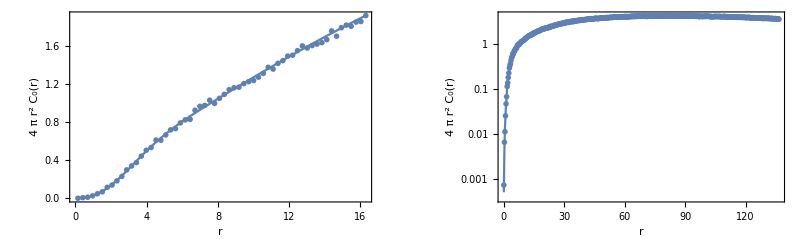

```mathematica
data=SelectFirst[simulations,#[[1]]==c&][[2]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, 0][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, 0][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, Rayleigh scattering, Gamma-6 random flight - correlated emission\nCollision-rate density C_0[r], c = "<>ToString[c]]
```

## Namespace

```mathematica
End[]
```

inf3DisopointRayleighscatterGamma6`